```mathematica
(* Some boring setup things. *)
SetDirectory[NotebookDirectory[]];
Colours=Lookup["DefaultPlotStyle"]@Lookup[Method]@Charting`ResolvePlotTheme[Automatic,Plot];

AbsErr[Data_,Real_]:=Data-Real;
RelErr[Data_,Real_]:=(Data-Real)/Real;

AtomDist=ProbabilityDistribution[{"CDF", UnitStep[x]}, {x,-∞,∞}];

(* Convert a defective PDF to a full PDF by adding an atom at 0. *)
CompletePDF[g_,p0_]:=Function[x,p0*PDF[AtomDist,x]+g[x]];

(*
  Approximate the random sum X = ∑_(k=1)^N Subscript[U, k] by a mixture distribution. We truncate N to (0,NMax) so that Pr(N ≤ NMax) ≥ 0.999. The resulting distribution normally allows for easy simulation (maybe a little slow if NMax is huge),CDF calculation (if Subscript[U, 1]+Subscript[U, 2] has a simple distribution), but has no PDF evaluation.
*)
CompoundDistribution[NDist_,UDist_,NMin_:1,NMax_:∞,IncludeZero_:True]:=Module[{Components,Weights,Cutoff=1-E^-5,NumComps},
NumComps=If[NumericQ[InverseCDF[NDist,0.999]],Min[Ceiling[InverseCDF[NDist, 0.999]],NMax],NMax];
NumComps=Max[NumComps,NMin];

Print["Using ", NumComps , " non-degenerate components in the mixture."];
Weights=PDF[NDist, Range[If[IncludeZero,0,1],NumComps]];
Components=Map[TransformedDistribution[Sum[Subscript[X, i],{i,#}],Table[Subscript[X, i] \[Distributed]UDist,{i,#}]]&,Range[NumComps]];
If[IncludeZero,PrependTo[Components,AtomDist]];
Return[MixtureDistribution[Weights,Components]];
];

(* Sample R iid replicates of X = ∑_(k=1)^N Subscript[U, k]. This will be slow. *)
RandomCompoundSum[NDist_,UDist_,R_]:=Module[{Ns},
Ns=RandomVariate[NDist,R];
Table[Total[RandomVariate[UDist,Ns[[i]]]],{i,R}]
];

ReferenceCMC[NDist_,UDist_,xs_,as_,R_:10]:=Module[{Ss,CrudeDist,SLP,Verbose=R>10^6},
If[Verbose,Print["Starting simulating..."]];
Ss=RandomCompoundSum[NDist,UDist,R];
If[Verbose,Print["Constructing distribution..."]];
CrudeDist=EmpiricalDistribution[Ss];
If[Verbose,Print["Finding SLP function..."]];
SLP[a_]=Mean@Table[Max[Ss[[i]]-a,0],{i,R}];
If[Verbose,Print["Calculating over the grid..."]];
{SurvivalFunction[CrudeDist,xs],SLP /@ as}
];

(* Renaming commonly used attributed of the gamma distribution & function. *)
Γ=Gamma;
γ[r_,m_,x_]:=PDF[GammaDistribution[r,m],x];
Γl[r_,m_,x_]:=CDF[GammaDistribution[r,m],x];
Γu[r_,m_,x_]:=SurvivalFunction[GammaDistribution[r,m],x];

(* Create the list {Subscript[q̃, 1,k],...,Subscript[q̃, k,k]} using Lemma 1 of our paper. *)
qTildes[r_,k_]:=√(Γ[k+r]/(Γ[r]Γ[k+1]))Table[(-1)^(k+i) Binomial[k,i]  ,{i,0,k}];

(* The Subscript[c, k] coefficients from (38) in our paper. *)
cCoeff[r_,k_]:=√(Γ[k+r]/(Γ[k+1]Γ[r]))

PGF[NDist_,s_]:=MomentGeneratingFunction[NDist,Log[s]];

(* Find the Subscript[q, k] coefficients for the orthogonal Gamma expansion of X = ∑_(k=1)^N Subscript[U, k]. *)
OrthoGammaCoeffs[NDist_,UDist_,r_,m_,K_,Verbosity_:1,LTofU_:None,Tilt_:0]:=Module[{Coeffs,LTofSN,LT,CGF,TaylorCGF,c},
If[Verbosity≥ 3,Print["Starting OrthoGammaCoeffs..." ]];

(* Laplace transforms of Subscript[f, S_N] and e^(-Tilt x) Subscript[f, S_N]^+. *)
LTofSN[t_]=PGF[NDist,If[LTofU=!= None,LTofU[t],MomentGeneratingFunction[UDist,-t]]];
LT[t_]=LTofSN[t+Tilt]-PDF[NDist,0];

If[Verbosity≥ 3,Print["Lap trans of e^(-Tilt x) f_X^+", LT[t], " at 0 is ", LT[0]//N ]];

(*Generating Function of the coefficients of the expansion*)
CGF[z_]=(1+z)^-r LT[-z/(m (1+z))];

(*To Print the coefficients or not to print the coefficients*)
If[Verbosity≥ 3,Print["C[z]=",CGF[z]]];

(*Taylor Development arround 0 of the generating function of the coefficients*)
TaylorCGF[z_]=Normal[Series[CGF[z],{z,0,K}]];
If[Verbosity≥3 ,Print["Taylor[z]=",N@TaylorCGF[z]]];

(*Coefficients of the expansion*)
c= Table[cCoeff[r,k],{k,0,K}];
PadRight[CoefficientList[TaylorCGF[z],z],K+1]/c
]; 

PseudoGammaCoeffsIndirectly[NDist_,UDist_,r_,m_,K_,Verbosity_:1,LTofU_:None,Tilt_:0]:=Module[{qs,KChop,Small,Ind,pLemma,ps,pFix},
If[Verbosity≥ 3,Print["Starting PseudoGammaCoeffsIndirectly..."]];
qs=OrthoGammaCoeffs[NDist,UDist,r,m,K,Verbosity,LTofU,Tilt];

(* Chop off the q's when they start getting consistently small. *)
AbsoluteTiming[Small=Map[#<0 &,Abs@N[qs]]];
Ind=SequencePosition[Small,ConstantArray[True,8]];

KChop=If[Length[Ind]== 0,K,
qs=qs[[1;;First@First@Ind-1]];
 Length[qs]-1];
If[Verbosity≥ 1 && KChop<K,Print["Effective K is ", KChop, " original was ", K]];

If[Verbosity≥ 1,Print["N@qs are ",N@qs]];
pLemma[i_]=If[r== 1,
Sum[Subscript[q, k] (-1)^(k+i) Binomial[k,i],{k,i,KChop}],
Sum[Subscript[q, k] (-1)^(k+i)/(i! (k-i)!) √((k! Gamma[k+r])/Gamma[r]),{k,i,KChop}]];
ps=Table[0,{i,0,KChop}];

For[i=0,i≤ KChop,i++,
ps[[i+1]]=pLemma[i]/(1-m Tilt)^(r+i)
];

Repl=Table[Subscript[q, k]-> qs[[k+1]],{k,0,KChop}];

For[i=0,i≤KChop,i++,
ps[[i+1]]=ps[[i+1]]/.Repl
];

ps
]; 

TransformInversion[LT_,x_,a_:18.5,M1_:10,M2_:10]:=Module[{Ss},
Ss=E^(a/2)/x Table[(-1)^k Re[LT[(a+I *2π k)/(2 x)]],{k,0,M1+M2}];
Ss[[1]]/=2;
Ss=Accumulate[Ss];

Sum[Binomial[M1,k] 2^-M1 Ss[[M2+k+1]],{k,0,M1}]
];

LaplaceInversionMethod[NDist_,UDist_,LTofU_:None]:=Module[{LTsum,LTsumstar,LTcdf,LTsvf,cdf,svf,cdfStar,svfStar},
(* Laplace transform of Subscript[S, N] *)
LTsum[t_]=PGF[NDist,If[LTofU=!=None,LTofU[t],MomentGeneratingFunction[UDist,-t]]];

cdf[x_]:=TransformInversion[LTsum[#]/# &,x];
svf[x_]:=TransformInversion[(1-LTsum[#])/# &,x];

(* Laplace transform of Subscript[S, N]^*, needed for stop-loss premiums. *)
LTsumstar[t_]=(1-LTsum[t])/(t Mean[NDist]Mean[UDist]);

cdfStar[x_]:=TransformInversion[LTsumstar[#]/# &,x];
svfStar[x_]:=TransformInversion[(1-LTsumstar[#])/# &,x];

{cdf,svf,cdfStar,svfStar}
];
```

Test 0: Negative Binomial / Exponential.

```mathematica
SeedRandom[1];
```

```mathematica
(* Problem description *)
α=10;p=3/4;λ=6;

(* Accuracy parameters *)
 K=α-1;R=10^6;numPoints=100;

(* This is the original problem, but it will soon be replaced. *)
NDist=NegativeBinomialDistribution[α,p];
UDist=ExponentialDistribution[λ];

(* Lemma 2 means we can instead use: *)
NDist=BinomialDistribution[α,1-p];
UDist=ExponentialDistribution[p λ];

(* Calculate the real distribution. *)
Print["Get the real distribution."];
RealDist=CompoundDistribution[NDist,UDist,α,α,True];
RealSVF[x_]=SurvivalFunction[RealDist,x];
RealSLP[a_]=Expectation[Max[S-a,0],S\[Distributed]RealDist,Assumptions->a>0];

(* Orthogonal polynomial method *)
r=1; m=1/(p λ);

Print["Get the ps using the qs."]
ps=PseudoGammaCoeffsIndirectly[NDist,UDist,r,m,K,2];

Print["Converting ps to machine prec."];
For[i=0,i≤ K,i++,
If[Mod[i,5]== 0, Print["Converting p_i for i = ",i]];
ps[[i+1]]=N[ps[[i+1]]]
];
Print["N@ps are ", N@ps, " first is ", First@ps];
Print["Total ps are ", N@Total[ps], " and the sum is ",N@ Sum[ps[[i]],{i,Length[ps]}]];

OrthoSVF[x_]=Sum[ps[[i+1]] Γu[r+i,m,x],{i,0,K}]//Refine[#,x>0]&//Simplify;
OrthoSLP[a_]=Sum[ps[[i+1]] (m(r+i)Γu[r+i+1,m,a]-a Γu[r+i,m,a]),{i,0,K}]//Refine[#,a>0]&//Simplify;

(* Make the grids to evaluate over, and some helper functions. *)
(*xMax=10*Mean[NDist]*Mean[UDist];dx=xMax/numPoints;xs=Table[i,{i,dx,xMax,dx}];
aMax=5*Mean[NDist]*Mean[UDist];da=aMax/numPoints;as=Table[i,{i,da,aMax,da}];*)
xs=Table[i/2,{i,5}];as=Table[i/2,{i,5}];

WithX[Data_]:=Transpose[{xs,Data}];
WithA[Data_]:=Transpose[{as,Data}];

(* Get the true values on these points. *)
RealSVFs=RealSVF/@xs;
RealSLPs=RealSLP/@as;

(* Orthogonal expansion on these points. *)
OrthoSVFs=OrthoSVF/@xs;
OrthoSLPs=OrthoSLP/@as;

(* Laplace inversion method. *)
{cdfI,svfI,cdfStarI,svfStarI}=LaplaceInversionMethod[NDist,UDist];

LapInvSVFs=Table[svfI[x],{x,xs}];
LapInvSLPs= Mean[NDist]Mean[UDist]Table[svfStarI[a],{a,as}];

(* Get some CMC answer. *)
(*Print["Doing CMC with R = 10^", Log10[R]];
Print["That took ", First@AbsoluteTiming[{CrudeSVFs,CrudeSLPs}= ReferenceCMC[NDist,UDist,xs,as,R];]," seconds"];*)

(***** Make the plots *****)
RefName="Real";
EstNames={"Crude MC (R = 10^" <> ToString[Log10[R]]<>")","Orthogonal (K = "<>ToString[K]<>")","Laplace Inversion"};
RefSVFs=RealSVFs;RefSLPs=RealSLPs;
AllSVFs={CrudeSVFs,OrthoSVFs,LapInvSVFs};
AllSLPs={CrudeSLPs,OrthoSLPs,LapInvSLPs};

(*SVFEst=ListPlot[WithX/@Append[AllSVFs,RefSVFs],Joined->True,AspectRatio->1/3];
SVFAbsErr=ListPlot[WithX[AbsErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];
SVFRelErr=ListPlot[WithX[RelErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];
SVFPlot=Legended[GraphicsColumn[{SVFEst, SVFAbsErr,SVFRelErr}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["exponential_svf.pdf",SVFPlot];

SLPEst=ListPlot[WithA/@Append[AllSLPs,RefSLPs],Joined->True,AspectRatio->1/3];
SLPAbsErr=ListPlot[WithA[AbsErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];
SLPRelErr=ListPlot[WithA[RelErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];
SLPPlot=Legended[GraphicsColumn[{SLPEst, SLPAbsErr,SLPRelErr}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["exponential_slp.pdf",SLPPlot];*)
```

Get the real distribution.

Using 10 non-degenerate components in the mixture.

Get the ps using the qs.

N@qs are {0.943686,1.55631,1.25619,0.618814,0.201499,0.0445948,0.00667477,0.000649452,0.0000371933,9.53674×10^-7}

Converting ps to machine prec.

Converting p_i for i = 0

Converting p_i for i = 5

N@ps are {0.187712,0.281568,0.250282,0.145998,0.0583992,0.016222,0.0030899,0.000386238,0.0000286102,9.53674×10^-7} first is 0.187712

Total ps are 0.943686 and the sum is 0.943686

```mathematica
RelErr[LapInvSVFs,RefSVFs]
RelErr[LapInvSLPs,RefSLPs]
```

{7.27395×10^-7,1.92151×10^-6,5.86327×10^-6,0.0000177669,0.0000401774}

{8.67707×10^-7,2.26679×10^-6,5.9165×10^-6,0.0000112371,-0.0000211675}

Test 1: Poisson / Gamma.

```mathematica
SeedRandom[1];
```

Get the truncated distribution.

Using 250 non-degenerate components in the mixture.

Getting truncated SVF.

Getting truncated SLP

Get the ps using the qs.

N@qs are {0.864665,0.148252,-0.155488,0.0594578,-0.0115797,-0.00038479,-0.00078936,0.00404098,-0.00614915,0.00694044,-0.00693772,0.00658843,-0.00614092,0.00570091,-0.0053007,0.004943,-0.00462197}

Converting ps to machine prec.

Converting p_i for i = 0

Converting p_i for i = 5

Converting p_i for i = 10

Converting p_i for i = 15

Calculating the ps took this long: 0.0589259

ps are {0.361918,1.66595,-5.32414,17.4064,-44.4782,87.3275,-134.751,165.786,-163.609,129.468,-81.6466,40.515,-15.4828,4.39933,-0.875669,0.109002,-0.00638826}

Total ps are 0.864665 and the sum is 0.864665

Doing CMC with R = 10^6

That took 129.411 seconds

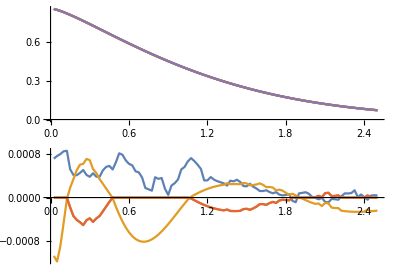

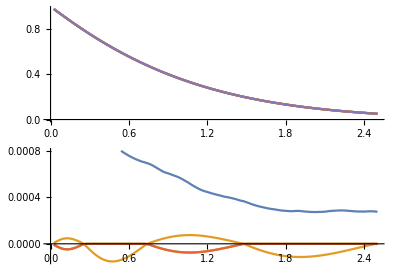

```mathematica
(* Accuracy parameters *)
 K=16;R=10^6;numPoints=100;TruncOrder=250;

(* Problem description *)
λ=2;rU=3/2;mU=1/3;
NDist=PoissonDistribution[λ];
UDist=GammaDistribution[rU,mU];

(* Calculate an approximate distribution. *)
Print["Get the truncated distribution."];
TruncDist=CompoundDistribution[NDist,UDist,TruncOrder,TruncOrder,True];
Print["Getting truncated SVF."]
TruncSVF[x_]=SurvivalFunction[TruncDist,x];

Print["Getting truncated SLP"]
Template[a_]=Expectation[Max[S-a,0],S\[Distributed]GammaDistribution[r,m],Assumptions->a>0&&r>0&&m>0];
TruncSLP[a_]=Sum[PDF[NDist,n] Template[a]/.{r-> n rU,m-> mU},{n,1,TruncOrder-1}];
(* Orthogonal polynomial method *)
(*r=1;m=λ Mean[UDist];
Print["m using 1-moment magic is ", N@m];*)
r=λ Mean[UDist]^2/Moment[UDist,2];
m=Moment[UDist,2]/Mean[UDist];

Print["Get the ps using the qs."]
ps=PseudoGammaCoeffsIndirectly[NDist,UDist,r,m,K];

Print["Converting ps to machine prec."];
For[i=0,i≤ K,i++,
If[Mod[i,5]== 0, Print["Converting p_i for i = ",i]];
ps[[i+1]]=N[ps[[i+1]]]
];

Print["ps are ", ps];
Print["Total ps are ", Total[ps], " and the sum is ",Sum[ps[[i]],{i,Length[ps]}]];

OrthoSVF[x_]=Sum[ps[[i+1]] Γu[r+i,m,x],{i,0,K}]//Refine[#,x>0]&//Simplify;
OrthoSLP[a_]=Sum[ps[[i+1]] (m(r+i)Γu[r+i+1,m,a]-a Γu[r+i,m,a]),{i,0,K}]//Refine[#,a>0]&//Simplify;

(* Make the grids to evaluate over, and some helper functions. *)
xMax=2.5*Mean[NDist]*Mean[UDist];dx=xMax/numPoints;xs=Table[i,{i,dx,xMax,dx}];
aMax=2.5*Mean[NDist]*Mean[UDist];da=aMax/numPoints;as=Table[i,{i,da,aMax,da}];

WithX[Data_]:=Transpose[{xs,Data}];
WithA[Data_]:=Transpose[{as,Data}];

(* Get the truncated values on these points. *)
TruncSVFs=TruncSVF/@xs;
TruncSLPs=TruncSLP/@as;

(* Orthogonal expansion on these points. *)
OrthoSVFs=OrthoSVF/@xs;
OrthoSLPs=OrthoSLP/@as;

(* Laplace inversion method. *)
{cdfI,svfI,cdfStarI,svfStarI}=LaplaceInversionMethod[NDist,UDist];

LapInvSVFs=Table[svfI[x],{x,xs}];
LapInvSLPs= Mean[NDist]Mean[UDist]Table[svfStarI[a],{a,as}];

(* Get some CMC answer. *)
Print["Doing CMC with R = 10^", Log10[R]];
Print["That took ", First@AbsoluteTiming[{CrudeSVFs,CrudeSLPs}= ReferenceCMC[NDist,UDist,xs,as,R];]," seconds"];

(***** Make the plots *****)
EstNames={"Crude MC (R = 1e" <> ToString[Log10[R]]<>")","Orthogonal (K = "<>ToString[K]<>")","Laplace Inversion","Truncated (Order = "<>ToString[TruncOrder]<>")"};
AllSVFs={CrudeSVFs, OrthoSVFs,LapInvSVFs,TruncSVFs};
AllSLPs={CrudeSLPs,OrthoSLPs,LapInvSLPs, TruncSLPs};

RefName="Median";
RefSVFs=Table[Median[AllSVFs[[;;,i]]], {i,Length[xs]}];
RefSLPs=Table[Median[AllSLPs[[;;,i]]], {i,Length[xs]}];


SVFEst=ListPlot[WithX/@Append[AllSVFs,RefSVFs],Joined->True,AspectRatio->1/3];
SVFAbsErr=ListPlot[WithX[AbsErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];
(*SVFRelErr=ListPlot[WithX[RelErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];*)
SVFPlot=Legended[GraphicsColumn[{SVFEst, SVFAbsErr(*,SVFRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["poisson_gamma_svf.pdf",SVFPlot];

SLPEst=ListPlot[WithA/@Append[AllSLPs,RefSLPs],Joined->True,AspectRatio->1/3];
SLPAbsErr=ListPlot[WithA[AbsErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];
(*SLPRelErr=ListPlot[WithA[RelErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];*)
SLPPlot=Legended[GraphicsColumn[{SLPEst, SLPAbsErr(*,SLPRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["poisson_gamma_slp.pdf",SLPPlot];
```

Test 2: Pascal / Gamma.

```mathematica
SeedRandom[1];
```

```mathematica
(* Accuracy parameters *)
 K=16;R=10^6;numPoints=100;TruncOrder=250;

(* Problem description *)
α=10;p=1/6;rU=3/2;mU=1/75;
NDist=NegativeBinomialDistribution[α,p];
UDist=GammaDistribution[rU,mU];
(* Calculate an approximate distribution. *)
Print["Get the truncated distribution."];
TruncDist=CompoundDistribution[NDist,UDist,TruncOrder,TruncOrder,True];
Print["Getting truncated SVF."]
TruncSVF[x_]=SurvivalFunction[TruncDist,x];

Print["Getting truncated SLP"]
Template[a_]=Expectation[Max[S-a,0],S\[Distributed]GammaDistribution[r,m],Assumptions->a>0&&r>0&&m>0];
TruncSLP[a_]=Sum[PDF[NDist,n]*Template[a]/.{r-> n rU,m-> mU},{n,1,TruncOrder-1}];

(* Orthogonal polynomial method *)
r=1;
radOfConv=s/.First@Solve[MomentGeneratingFunction[UDist,s]== 1/(1-p),s];
m=1/radOfConv;
Print["m using absicca magic is ", N@m];

Print["Get the ps using the qs."]
ps=PseudoGammaCoeffsIndirectly[NDist,UDist,r,m,K];

Print["Converting ps to machine prec."];
For[i=0,i≤ K,i++,
If[Mod[i,5]== 0, Print["Converting p_i for i = ",i]];
ps[[i+1]]=N[ps[[i+1]]]
];
Print["ps are ", ps];
Print["Total ps are ", Total[ps], " and the sum is ",Sum[ps[[i]],{i,Length[ps]}]];

OrthoSVF[x_]=Sum[ps[[i+1]] Γu[r+i,m,x],{i,0,K}]//Refine[#,x>0]&//Simplify;
OrthoSLP[a_]=Sum[ps[[i+1]] (m(r+i)Γu[r+i+1,m,a]-a Γu[r+i,m,a]),{i,0,K}]//Refine[#,a>0]&//Simplify;

(* Make the grids to evaluate over, and some helper functions. *)
xMax=2.5*Mean[NDist]*Mean[UDist];dx=xMax/numPoints;xs=Table[i,{i,dx,xMax,dx}];
aMax=2.5*Mean[NDist]*Mean[UDist];da=aMax/numPoints;as=Table[i,{i,da,aMax,da}];

WithX[Data_]:=Transpose[{xs,Data}];
WithA[Data_]:=Transpose[{as,Data}];

(* Get the truncated values on these points. *)
TruncSVFs=TruncSVF/@xs;
TruncSLPs=TruncSLP/@as;

(* Orthogonal expansion on these points. *)
OrthoSVFs=OrthoSVF/@xs;
OrthoSLPs=OrthoSLP/@as;

(* Laplace inversion method. *)
{cdfI,svfI,cdfStarI,svfStarI}=LaplaceInversionMethod[NDist,UDist];

LapInvSVFs=Table[svfI[x],{x,xs}];
LapInvSLPs= Mean[NDist]Mean[UDist]Table[svfStarI[a],{a,as}];

(* Get some CMC answer. *)
Print["Doing CMC with R = 1e", Log10[R]];
Print["That took ", First@AbsoluteTiming[{CrudeSVFs,CrudeSLPs}= ReferenceCMC[NDist,UDist,xs,as,R];]," seconds"];
```

Get the truncated distribution.

Using 250 non-degenerate components in the mixture.

Getting truncated SVF.

Getting truncated SLP

m using absicca magic is 0.116498

Get the ps using the qs.

N@qs are {1.,7.58384,25.5856,50.3959,63.8652,53.9979,30.4591,11.0529,2.3412,0.220545,-3.8612×10^-9,3.79226×10^-9,-3.72584×10^-9,3.65984×10^-9,-3.59599×10^-9,3.5327×10^-9,-3.47138×10^-9}

Converting ps to machine prec.

Converting p_i for i = 0

Converting p_i for i = 5

Converting p_i for i = 10

Converting p_i for i = 15

ps are {3.65529×10^-7,9.36517×10^-6,0.000115482,0.001106,0.00727974,0.0348863,0.116854,0.26295,0.356213,0.220613,-0.0000433453,0.000021628,-8.30382×10^-6,2.36891×10^-6,-4.73152×10^-7,5.90747×10^-8,-3.47138×10^-9}

Total ps are 1. and the sum is 1.

Doing CMC with R = 1e6

That took 189.496 seconds

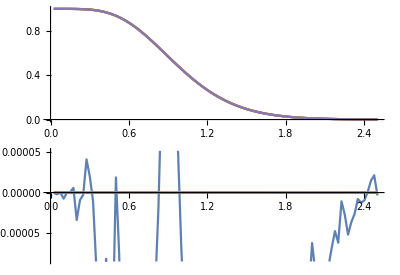

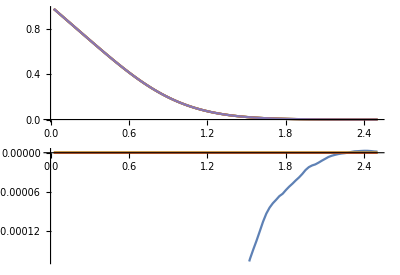

```mathematica
(***** Make the plots *****)
EstNames={"Crude MC (R = 1e" <> ToString[Log10[R]]<>")","Orthogonal (K = "<>ToString[K]<>")","Laplace Inversion","Truncated (Order = "<>ToString[TruncOrder]<>")"};
AllSVFs={CrudeSVFs, OrthoSVFs,LapInvSVFs,TruncSVFs};
AllSLPs={CrudeSLPs,OrthoSLPs,LapInvSLPs, TruncSLPs};

RefName="Median";
RefSVFs=Table[Median[AllSVFs[[;;,i]]], {i,Length[xs]}];
RefSLPs=Table[Median[AllSLPs[[;;,i]]], {i,Length[xs]}];

SVFEst=ListPlot[WithX/@Append[AllSVFs,RefSVFs],Joined->True,AspectRatio->1/3];
SVFAbsErr=ListPlot[WithX[AbsErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];
(*SVFRelErr=ListPlot[WithX[RelErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];*)
SVFPlot=Legended[GraphicsColumn[{SVFEst, SVFAbsErr(*,SVFRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["pascal_gamma_svf.pdf",SVFPlot];

SLPEst=ListPlot[WithA/@Append[AllSLPs,RefSLPs],Joined->True,AspectRatio->1/3];
SLPAbsErr=ListPlot[WithA[AbsErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];
(*SLPRelErr=ListPlot[WithA[RelErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];*)
SLPPlot=Legended[GraphicsColumn[{SLPEst, SLPAbsErr(*,SLPRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["pascal_gamma_slp.pdf",SLPPlot];
```

Test 3: Poisson / Pareto.

```mathematica
SeedRandom[1];
```

Want to take m > 1/2 Tilt i.e. 1/2 > 1/2

Tilting by 1. which gives a modified m of 1.

Get the ps using the qs.

N@qs are {0.253186,0.481835,0.174534,-0.00792313,-0.00734867,0.00496739,-0.00282642,0.00206579,-0.00173445,0.00153825,-0.00138398,0.00125355,-0.00116346,0.00102712,-0.00107824,0.000733524,-0.000906132}

Converting ps to machine prec.

Converting p_i for i = 0

Converting p_i for i = 5

Converting p_i for i = 10

Converting p_i for i = 15

ps are {0.0152153,0.582389,-1.34385,11.7161,-55.0614,207.427,-627.396,1527.21,-2996.9,4731.46,-5968.96,5939.24,-4561.45,2610.67,-1049.08,264.261,-31.4176}

Total ps are 0.981263 and the sum is 0.981263

Memory problem...

Memory problem...

Memory problem...

«1 more identical outputs»

Doing CMC with R = 10^6

That took 463.59 seconds

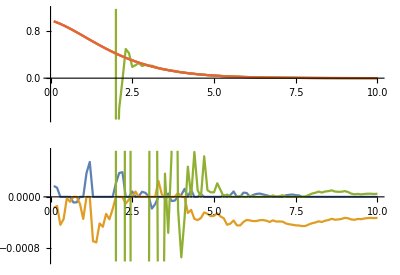

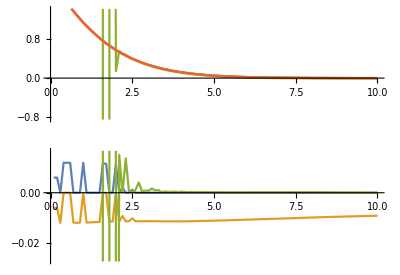

```mathematica
(* Accuracy parameters *)
K=16;R=10^6;numPoints=100;

(* Problem description *)
λ=4;a=5;b=11;θ=0;

NDist=PoissonDistribution[λ];
UDist=ParetoDistribution[a,b,θ];
LTofU[s_]=Expectation[E^(-s X),X\[Distributed]UDist];

(* Orthogonal polynomial method *)
Tilt=1;
ThetaFracOfM=1/2;
mOrig=ThetaFracOfM/Tilt;

r=Mean[UDist];
m = mOrig/(1-mOrig Tilt);

Print["Want to take m > 1/2 Tilt i.e. ", mOrig, " > " ,1/(2 Tilt)];
Print["Tilting by ", N@Tilt, " which gives a modified m of ", N@m];

Print["Get the ps using the qs."];
ps=PseudoGammaCoeffsIndirectly[NDist,UDist,r,mOrig,K,2,LTofU,Tilt];
Print["Converting ps to machine prec."];
For[i=0,i≤ K,i++,
If[Mod[i,5]== 0, Print["Converting p_i for i = ",i]];
ps[[i+1]]=N[ps[[i+1]]]
];
Print["ps are ",ps];
Print["Total ps are ", Total[ps], " and the sum is ",Sum[ps[[i]],{i,Length[ps]}]];

OrthoSVF[x_]= Sum[ps[[i+1]] Γu[r+i,m,x],{i,0,K}]//Refine[#,x>0]&;
OrthoSLP[a_]= Sum[ps[[i+1]] (m(r+i)Γu[r+i+1,m,a]-a Γu[r+i,m,a]),{i,0,K}]//Refine[#,a>0]&;
(* Make the grids that the Laplace inversion will evaluate on. *)
xMax=5.0*Mean[NDist]*Mean[UDist];dx=xMax/numPoints;xs=Table[i,{i,dx,xMax,dx}];
aMax=5.0*Mean[NDist]*Mean[UDist];da=aMax/numPoints;as=Table[i,{i,da,aMax,da}];

WithX[Data_]:=Transpose[{xs,Data}];
WithA[Data_]:=Transpose[{as,Data}];

(* Orthogonal expansion on these points. *) 
OrthoSVFs=OrthoSVF/@xs;
OrthoSLPs=OrthoSLP/@as;

(* Laplace inversion method. *)
{cdfI,svfI,cdfStarI,svfStarI}=LaplaceInversionMethod[NDist,UDist,LTofU];

(*LapInvSVFs=Table[svfI[x],{x,xs}];*)
LapInvSVFs=Table[
svf=Quiet@Catch[svfI[x],_SystemException];
If[svf=== SystemException["MemoryAllocationFailure"],Print["Memory problem..."];svf=Indeterminate];
svf,{x,xs}];

(*LapInvSLPs= Mean[NDist]Mean[UDist]Table[svfStarI[a],{a,as}];*)
svfStars=Table[
star=Quiet@Catch[svfStarI[a],_SystemException];
If[star=== SystemException["MemoryAllocationFailure"],Print["Memory problem..."];star=Indeterminate];
star,{a,as}];
LapInvSLPs= Mean[NDist]Mean[UDist]*svfStars;

(* Get some CMC answer. *)
Print["Doing CMC with R = 10^", Log10[R]];
Print["That took ", First@AbsoluteTiming[{CrudeSVFs,CrudeSLPs}= ReferenceCMC[NDist,UDist,xs,as,R];]," seconds"];

(***** Make the plots *****)
EstNames={"Crude MC (R = 1e" <> ToString[Log10[R]]<>")","Orthogonal (K = "<>ToString[K]<>")","Laplace Inversion"};
AllSVFs={CrudeSVFs, OrthoSVFs,LapInvSVFs};
AllSLPs={CrudeSLPs,OrthoSLPs,LapInvSLPs};
RefName="Median";
RefSVFs=Table[Median[DeleteCases[AllSVFs[[;;,i]],Indeterminate]], {i,Length[xs]}];
RefSLPs=Table[Median[DeleteCases[AllSLPs[[;;,i]],Indeterminate]], {i,Length[xs]}];

SVFEst=ListPlot[WithX/@Append[AllSVFs,RefSVFs],Joined->True,AspectRatio->1/3];
SVFAbsErr=ListPlot[WithX[AbsErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];
(*SVFRelErr=ListPlot[WithX[RelErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];*)
SVFPlot=Legended[GraphicsColumn[{SVFEst, SVFAbsErr(*,SVFRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["poisson_pareto_svf.pdf",SVFPlot];

SLPEst=ListPlot[WithA/@Append[AllSLPs,RefSLPs],Joined->True,AspectRatio->1/3];
SLPAbsErr=ListPlot[WithA[AbsErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];
(*SLPRelErr=ListPlot[WithA[RelErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];*)
SLPPlot=Legended[GraphicsColumn[{SLPEst, SLPAbsErr(*,SLPRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["poisson_pareto_slp.pdf",SLPPlot];
```

Test 4: Pascal / Weibull .

```mathematica
SeedRandom[1];
```

Want to take m > 1/2 Tilt i.e. 1/2 > 1/2

Tilting by 1. which gives a modified m of 1.

Get the ps using the qs.

N@qs are {0.179459,0.042885,0.0868164,0.0173474,0.0534309,0.00361812,0.0360942,-0.00365071,0.0262684,-0.00740137,0.020412,-0.00923628,0.0167695,-0.0100313,0.0144062,-0.0102674,0.0128041}

Converting ps to machine prec.

Converting p_i for i = 0

Converting p_i for i = 5

Converting p_i for i = 10

Converting p_i for i = 15

21.4021

ps are {0.846394,-7.96457,73.4442,-491.522,2496.73,-9849.51,30703.,-76407.,152509.,-244009.,311064.,-312034.,241118.,-138610.,55866.5,-14099.,1678.26}

Total ps are 0.939448 and the sum is 0.939448

Doing CMC with R = 10^6

That took 149.906 seconds

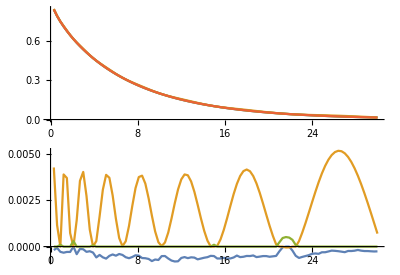

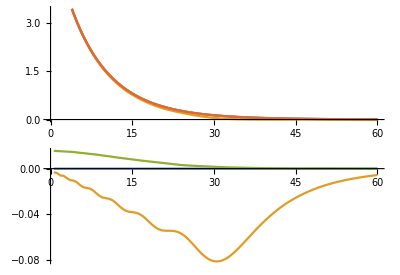

```mathematica
K=16;R=10^6;numPoints=100;

(* Problem description *)
α=2;p=1/4;β=1/2;λ=1/2;
(*α=10;p=1/6;λ=1/100;*)
NDist=NegativeBinomialDistribution[α,p];
UDist=WeibullDistribution[β,λ];
LTofU[s_]=Expectation[E^(-s X),X\[Distributed]UDist];

(* Orthogonal polynomial method *)
Tilt=1;
ThetaFracOfM=1/2;
mOrig=ThetaFracOfM/Tilt;

r=Mean[UDist];

m = mOrig/(1-mOrig Tilt);

Print["Want to take m > 1/2 Tilt i.e. ", mOrig, " > " ,1/(2 Tilt)];
Print["Tilting by ", N@Tilt, " which gives a modified m of ", N@m];

Print["Get the ps using the qs."];
ps=PseudoGammaCoeffsIndirectly[NDist,UDist,r,mOrig,K,2,LTofU,Tilt];Print["Converting ps to machine prec."];
Print[First@AbsoluteTiming[
For[i=0,i≤ K,i++,
If[Mod[i,5]== 0, Print["Converting p_i for i = ",i]];
ps[[i+1]]=N[ps[[i+1]]];
];
]];

Print["ps are ", ps];
Print["Total ps are ", Total[ps], " and the sum is ",Sum[ps[[i]],{i,Length[ps]}]];

OrthoSVF[x_]= Sum[ps[[i+1]] Γu[r+i,m,x],{i,0,K}]//Refine[#,x>0]&;
OrthoSLP[a_]= Sum[ps[[i+1]] (m(r+i)Γu[r+i+1,m,a]-a Γu[r+i,m,a]),{i,0,K}]//Refine[#,a>0]&;

(* Make the grids that the Laplace inversion will evaluate on. *)
xMax=5*Mean[NDist]*Mean[UDist];dx=xMax/numPoints;xs=Table[i,{i,dx,xMax,dx}];
aMax=10*Mean[NDist]*Mean[UDist];da=aMax/numPoints;as=Table[i,{i,da,aMax,da}];

WithX[Data_]:=Transpose[{xs,Data}];
WithA[Data_]:=Transpose[{as,Data}];

(* Orthogonal expansion on these points. *)
OrthoSVFs=OrthoSVF/@xs;
OrthoSLPs=OrthoSLP/@as;

(* Laplace inversion method. *)
{cdfI,svfI,cdfStarI,svfStarI}=LaplaceInversionMethod[NDist,UDist,LTofU];

LapInvSVFs=Table[svfI[x],{x,xs}];
LapInvSLPs= Mean[NDist]Mean[UDist]Table[svfStarI[a],{a,as}];

(* Get some CMC answer. *)
Print["Doing CMC with R = 10^", Log10[R]];
Print["That took ", First@AbsoluteTiming[{CrudeSVFs,CrudeSLPs}= ReferenceCMC[NDist,UDist,xs,as,R];]," seconds"];

(***** Make the plots *****)
EstNames={"Crude MC (R = 1e" <> ToString[Log10[R]]<>")","Orthogonal (K = "<>ToString[K]<>")","Laplace Inversion"};
AllSVFs={CrudeSVFs, OrthoSVFs,LapInvSVFs};
AllSLPs={CrudeSLPs,OrthoSLPs,LapInvSLPs};

RefName="Median";
RefSVFs=Table[Median[AllSVFs[[;;,i]]], {i,Length[xs]}];
RefSLPs=Table[Median[AllSLPs[[;;,i]]], {i,Length[xs]}];

SVFEst=ListPlot[WithX/@Append[AllSVFs,RefSVFs],Joined->True,AspectRatio->1/3];
SVFAbsErr=ListPlot[WithX[AbsErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];
(*SVFRelErr=ListPlot[WithX[RelErr[#,RefSVFs]]&/@AllSVFs,Joined->True,AspectRatio->1/3];*)
SVFPlot=Legended[GraphicsColumn[{SVFEst, SVFAbsErr(*,SVFRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["pascal_weibull_svf.pdf",SVFPlot];

SLPEst=ListPlot[WithA/@Append[AllSLPs,RefSLPs],Joined->True,AspectRatio->1/3];
SLPAbsErr=ListPlot[WithA[AbsErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];
(*SLPRelErr=ListPlot[WithA[RelErr[#,RefSLPs]]&/@AllSLPs,Joined->True,AspectRatio->1/3];*)
SLPPlot=Legended[GraphicsColumn[{SLPEst, SLPAbsErr(*,SLPRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["pascal_weibull_slp.pdf",SLPPlot];
```

Test 5: Ruin probability: Poisson / Exponential.

```mathematica
SeedRandom[1];
```

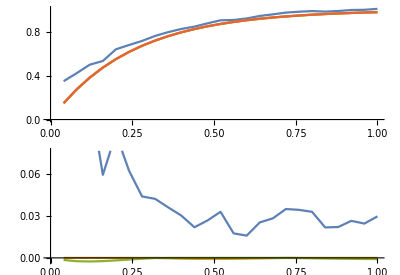

```mathematica
(* Accuracy parameters *)
K=16;R=10^5;numPoints=25;

(* Problem description *)
c=1;λ=4;UDist=ExponentialDistribution[4];UDist=GammaDistribution[2,2];

(* Time grid *)
tMax=1;
dt=tMax/numPoints;ts=Table[i,{i,dt,tMax,dt}];

(* Orthogonal polynomial method *)
Verbosity=0;

SLPs=Table[
NDist=PoissonDistribution[λ t];

r=λ t Mean[UDist]^2/Moment[UDist,2];
m=Moment[UDist,2]/Mean[UDist];

SeedRandom[1];
ps=PseudoGammaCoeffsIndirectly[NDist,UDist,r,m,K,Verbosity];

OrthogonalSLP= Sum[ps[[i+1]] (m(r+i)Γu[r+i+1,m,c t]-c t  Γu[r+i,m,c t]),{i,0,K}];

SeedRandom[1];
CrudeSLP= First@Last@ReferenceCMC[NDist,UDist,{},{c t},R];

svfStarI=Last@LaplaceInversionMethod[NDist,UDist];
LapInvSLP= Mean[NDist]Mean[UDist]svfStarI[c t];

{OrthogonalSLP,LapInvSLP,CrudeSLP},{t,ts}];


OrthoRuins=1/(c ts)(λ ts *Mean[UDist]-SLPs[[;;,1]])//N;
LapInvRuins=1/(c ts)(λ ts *Mean[UDist]-SLPs[[;;,2]])//N;
CrudeRuins=1/(c ts)(λ ts *Mean[UDist]-SLPs[[;;,3]])//N;


(***** Make the plots *****)
EstNames={"Crude MC (R = 1e" <> ToString[Log10[R]]<>")","Orthogonal (K = "<>ToString[K]<>")","Laplace Inversion"};
AllRuins={CrudeRuins, OrthoRuins,LapInvRuins};

RefName="Median";
RefRuins=Table[Median[AllRuins[[;;,i]]], {i,Length[ts]}];

WithT[Data_]:=Transpose[{ts,Data}];

RuinEst=ListPlot[WithT/@Append[AllRuins,RefRuins],Joined->True,AspectRatio->1/3];
RuinAbsErr=ListPlot[WithT[AbsErr[#,RefRuins]]&/@AllRuins,Joined->True,AspectRatio->1/3];
(*RuinRelErr=ListPlot[WithA[RelErr[#,RefRuins]]&/@AllRuins,Joined->True,AspectRatio->1/3];*)
RuinPlot=Legended[GraphicsColumn[{RuinEst, RuinAbsErr(*,RuinRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["poisson_exponential_ruin.pdf",RuinPlot];
```

Test 6: Ruin probability: Poisson Pareto

```mathematica
SeedRandom[1];
```

Memory problem...

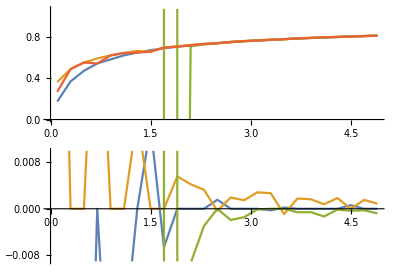

```mathematica
(* Accuracy parameters *)
K=16;R=10^5;numPoints=25;

(* Problem description *)
c=1;λ=2;a=5;b=11;θ=0;
UDist=ParetoDistribution[a,b,θ];
LTofU[s_]=Expectation[E^(-s X),X\[Distributed]UDist];

(* Time grid *)
tMax=5;
dt=tMax/numPoints;ts=Table[i,{i,10^-1,tMax,dt}];

(* Orthogonal polynomial method *)
Verbosity=0;

SLPs=Table[
NDist=PoissonDistribution[λ t];

(* Orthogonal polynomial method *)
Tilt=1;
ThetaFracOfM=1/2;
mOrig=ThetaFracOfM/Tilt;

r=Mean[UDist];
m = mOrig/(1-mOrig Tilt);

(*Print["Want to take m > 1/2 Tilt i.e. ", mOrig, " > " ,1/(2 Tilt)];
Print["Tilting by ", N@Tilt, " which gives a modified m of ", N@m];
*)
SeedRandom[1];
ps=PseudoGammaCoeffsIndirectly[NDist,UDist,r,mOrig,K,Verbosity,LTofU,Tilt];

OrthogonalSLP= Sum[ps[[i+1]] (m(r+i)Γu[r+i+1,m,c t]-c t  Γu[r+i,m,c t]),{i,0,K}];

SeedRandom[1];
CrudeSLP=First@Last@ReferenceCMC[NDist,UDist,{},{c t},R];

svfStarI=Last@LaplaceInversionMethod[NDist,UDist,LTofU];
(*LapInvSLP= Mean[NDist]Mean[UDist]svfStarI[c t];*)

LapInvSLP=Quiet@Catch[Mean[NDist]Mean[UDist]svfStarI[c t],_SystemException];
If[LapInvSLP=== SystemException["MemoryAllocationFailure"],Print["Memory problem..."];LapInvSLP=Indeterminate];

{OrthogonalSLP,LapInvSLP,CrudeSLP},{t,ts}];

OrthoRuins=1/(c ts)(λ ts *Mean[UDist]-SLPs[[;;,1]])//N;
LapInvRuins=1/(c ts)(λ ts *Mean[UDist]-SLPs[[;;,2]])//N;
CrudeRuins=1/(c ts)(λ ts *Mean[UDist]-SLPs[[;;,3]])//N;

(***** Make the plots *****)
EstNames={"Crude MC (R = 1e" <> ToString[Log10[R]]<>")","Orthogonal (K = "<>ToString[K]<>")","Laplace Inversion"};
AllRuins={CrudeRuins, OrthoRuins,LapInvRuins};

RefName="Median";
RefRuins=Table[Median[DeleteCases[AllRuins[[;;,i]],Indeterminate]], {i,Length[ts]}];

WithT[Data_]:=Transpose[{ts,Data}];

RuinEst=ListPlot[WithT/@Append[AllRuins,RefRuins],Joined->True,AspectRatio->1/3];
RuinAbsErr=ListPlot[WithT[AbsErr[#,RefRuins]]&/@AllRuins,Joined->True,AspectRatio->1/3];
(*RuinRelErr=ListPlot[WithA[RelErr[#,RefRuins]]&/@AllRuins,Joined->True,AspectRatio->1/3];*)
RuinPlot=Legended[GraphicsColumn[{RuinEst, RuinAbsErr(*,RuinRelErr*)}], LineLegend[Colours,Append[EstNames,RefName]]]
Export["poisson_pareto_ruin.pdf",RuinPlot];
```